```mathematica
SetDirectory[NotebookDirectory[]];
```

## age-dependent survival

```mathematica
Clear[ψ,κ]
fGompertzSurvival[t_,α_,β_]:=Exp[-α/β (Exp[β t]-1)]
fMeanGompertz[N_,t_,α_,β_,ψ_]:=If[N ψ fGompertzSurvival[t,α,β]>0.001,N ψ fGompertzSurvival[t,α,β],0.001]
fMeansGompertz[N_,lT__,α_,β_,ψ_]:=Table[fMeanGompertz[N,t,α,β,ψ],{t,lT}]
fGenerateSeriesGompertz[N_,lT__,α_,β_,ψ_,κ_]:=Module[{lMeans=fMeansGompertz[N,lT,α,β,ψ]},fGeneratePoint[#,κ]&/@lMeans]
fLogLikelihoodGompertz[y_,N_,t_,α_,β_,ψ_,κ_]:=LogLikelihood[fNegativeBinomialCustom[fMeanGompertz[N,t,α,β,ψ],κ],{y}]
fLogLikelihoodTotalGompertz[lY_,N_,lT_,α_,β_,ψ_,κ_]:=Total[fLogLikelihoodGompertz[#1,N,#2,α,β,ψ,κ]&@@@Thread[{lY,lT}]]
fMaximiseGompertz[lY__,lT__,N_Integer]:=Module[{lMax=NMaximize[{fLogLikelihoodTotalGompertz[lY,N,lT,α,β,ψ,κ],α>0,β>0.001,1>ψ>0,κ>0},{α,β,ψ,κ}][[2]]},{lMax[[1,2]],lMax[[2,2]],lMax[[3,2]],lMax[[4,2]]}]
fLifeGompertz[α_,β_]:=Exp[α/β] Gamma[0,α/β]/β
fLifetimeErrorGompertz[aAlphaTrue_,aBetaTrue_,lY__,lT__,N_Integer]:=Module[{lEst=Quiet[fMaximiseGompertz[lY,lT,N][[1;;2]]]},fLifeGompertz[aAlphaTrue,aBetaTrue]-fLifeGompertz[lEst[[1]],lEst[[2]]]]
fMCLifetimeErrorGompertz[α_,β_,ψ_,κ_,N_Integer,MaxT_]:=Module[{lY=fGenerateSeriesGompertz[N,Range@MaxT,α,β,ψ,κ]},fLifetimeErrorGompertz[α,β,lY,Range@MaxT,N]]
fSenescenceErrorGompertz[aAlphaTrue_,aBetaTrue_,lY__,lT__,N_Integer]:=Module[{lEst=Quiet[fMaximiseGompertz[lY,lT,N][[1;;2]]]},aBetaTrue-lEst[[2]]]
fMCSenescenceErrorGompertz[α_,β_,ψ_,κ_,N_Integer,MaxT_]:=Module[{lY=fGenerateSeriesGompertz[N,Range@MaxT,α,β,ψ,κ]},fSenescenceErrorGompertz[α,β,lY,Range@MaxT,N]]
fNegativeBinomialCustom[λ_,k_]:=Module[{n,p},p = k/(λ+k); n = (p λ)/(1-p); NegativeBinomialDistribution[n,p]]
fGeneratePoint[aMean_,aKappa_]:=RandomVariate[fNegativeBinomialCustom[aMean,aKappa],{1}][[1]]
fNegativeBinomialCustom[λ_,k_]:=Module[{n,p},p = k/(λ+k); n = (p λ)/(1-p); NegativeBinomialDistribution[n,p]]
fGeneratePoint[aMean_,aKappa_]:=RandomVariate[fNegativeBinomialCustom[aMean,aKappa],{1}][[1]]
fMean[N_,t_,λ_,ψ_]:=If[N ψ Exp[-λ t]>0.001,N ψ Exp[-λ t],0.001]
fMeans[N_,lT__,λ_,ψ_]:=Table[fMean[N,t,λ,ψ],{t,lT}]
fGenerateSeries[N_,lT__,λ_,ψ_,κ_]:=Module[{lMeans=fMeans[N,lT,λ,ψ]},fGeneratePoint[#,κ]&/@lMeans]
fLogLikelihood[y_,N_,t_,λ_,ψ_,κ_]:=LogLikelihood[fNegativeBinomialCustom[fMean[N,t,λ,ψ],κ],{y}]
fLogLikelihoodTotal[lY_,N_,lT_,λ_,ψ_,κ_]:=Total[fLogLikelihood[#1,N,#2,λ,ψ,κ]&@@@Thread[{lY,lT}]]
fMaximise[lY__,lT__,N_Integer]:=Module[{lMax=NMaximize[{fLogLikelihoodTotal[lY,N,lT,λ,ψ,κ],λ>0,1>ψ>0,κ>0},{λ,ψ,κ}][[2]]},{lMax[[1,2]],lMax[[2,2]],lMax[[3,2]]}]
fLifetimeError[aLambdaTrue_,lY__,lT__,N_Integer]:=Module[{aLambdaEst=Quiet[fMaximise[lY,lT,N][[1]]]},(1/aLambdaTrue)-(1/aLambdaEst)]
fMCLifetimeError[λ_,ψ_,κ_,N_Integer,MaxT_]:=Module[{lY=fGenerateSeries[N,Range@MaxT,λ,ψ,κ]},fLifetimeError[λ,lY,Range@MaxT,N]]
fMCLifetimeErrorSD[numReplicates_Integer,λ_,ψ_,κ_,N_Integer,MaxT_]:=Module[{lErrors=Table[fMCLifetimeError[λ,ψ,κ,N,MaxT],{i,1,numReplicates,1}]},StandardDeviation@lErrors]
fMCLifetimeErrorRMSE[numReplicates_Integer,λ_,ψ_,κ_,N_Integer,MaxT_]:=Module[{lErrors=Table[fMCLifetimeError[λ,ψ,κ,N,MaxT],{i,1,numReplicates,1}]},Sqrt@Mean[lErrors^2]]
fMCLifetimeErrorSD[numReplicates_Integer,λ_,ψ_,κ_,N_Integer,MaxT_]:=Module[{lErrors=Table[fMCLifetimeError[λ,ψ,κ,N,MaxT],{i,1,numReplicates,1}]},StandardDeviation@lErrors]
fMCLifetimeErrorRMSE[numReplicates_Integer,λ_,ψ_,κ_,N_Integer,MaxT_]:=Module[{lErrors=Table[fMCLifetimeError[λ,ψ,κ,N,MaxT],{i,1,numReplicates,1}]},Sqrt@Mean[lErrors^2]]
```

### Observed likelihood is what we are using to make information matrix! (Excited because now I know what to call this)

```mathematica
fSenescenceObservedLikelihoodSD[lY__,N_Integer,lT__,αEst_,βEst_,ψEst_,κEst_]:=Sqrt[-1/(D[fLogLikelihoodTotalGompertz[lY,N,lT,α,β,ψ,κ],{β,2}]/.{β->βEst,α->αEst,ψ->ψEst,κ->κEst})]
```

```mathematica
fSenescenceBeta[aAlphaTrue_,lY__,lT__,N_Integer]:=Module[{lEst=Quiet[fMaximiseGompertz[lY,lT,N][[1;;2]]]},lEst[[2]]]
```

```mathematica
fMCSenescencePowerGompertz[α_,β_,ψ_,κ_,N_Integer,MaxT_]:=Module[{lY=fGenerateSeriesGompertz[N,Range@MaxT,α,β,ψ,κ]},fSenescenceErrorGompertz[α,β,lY,Range@MaxT,N]]
```

### Alternative approach based on likelihood ratio comparing model with senescence to one without

```mathematica
fMaximiseValueGompertz[lY__,lT__,N_Integer]:=Module[{aMax=NMaxValue[{fLogLikelihoodTotalGompertz[lY,N,lT,α,β,ψ,κ],α>0.0001,β>0.001,0.2>ψ>0.001,κ>1},{α,β,ψ,κ}]},aMax]
fMaximiseValueExponential[lY__,lT__,N_Integer]:=Module[{aMax=NMaxValue[{fLogLikelihoodTotal[lY,N,lT,λ,ψ,κ],λ>0,1>ψ>0,κ>0},{λ,ψ,κ}]},aMax]
fMaximiseValueGompertz1[lY__,lT__,N_Integer]:=Module[{aMax=FindMaxValue[{fLogLikelihoodTotalGompertz[lY,N,lT,α,β,ψ,κ],α>0.0001,β>0.001,0.2>ψ>0.001,κ>1},{{α,0.1},{β,0.05},{ψ,0.03},{κ,4}}]},aMax]
```

```mathematica
fLikelihoodRatio[lY__,lT__,N_Integer]:=Module[{aMaxGompertz=fMaximiseValueGompertz1[lY,lT,N],aMaxExponential=fMaximiseValueExponential[lY,lT,N]},If[aMaxGompertz<aMaxExponential,0,2 (aMaxGompertz-aMaxExponential)]]
fMeanLifetimeGompertz[α_,β_]:=NIntegrate[Exp[-α/β (Exp[β t]-1)],{t,0,∞}]
```

```mathematica
fCalculateProportion[lLikelihood__,aThreshold_]:=N@Total[If[#>aThreshold,1,0]&/@lLikelihood]/Length@lLikelihood
fDifference[lLikelihood__,aPValue_]:=fCalculateProportion[lLikelihood,InverseCDF[ChiSquareDistribution[1],aPValue]]-aPValue
fCalculatePower[lLikelihood__]:=Quiet[FindRoot[fDifference[lLikelihood,p],{p,0.1}]]
fCalculatePowerCorrect[lLikelihood__,aSize_]:=N@Total[If[#>InverseCDF[ChiSquareDistribution[1],aSize],1,0]&/@lLikelihood]/Length@lLikelihood
```

```mathematica
lAlpha={0.15,0.051,0.019};
lBeta={0.063,0.34,0.6};
```

### Finding appropriate α and β values to yield a lifespan of 5 days

```mathematica
Manipulate[Plot[fGompertzSurvival[t,lAlpha[[i]],lBeta[[i]]],{t,0,20},PlotRange->{{0,28},{0,1}},PlotLabel->fMeanLifetimeGompertz[lAlpha[[i]],lBeta[[i]]]],{i,1,3,1}]
```

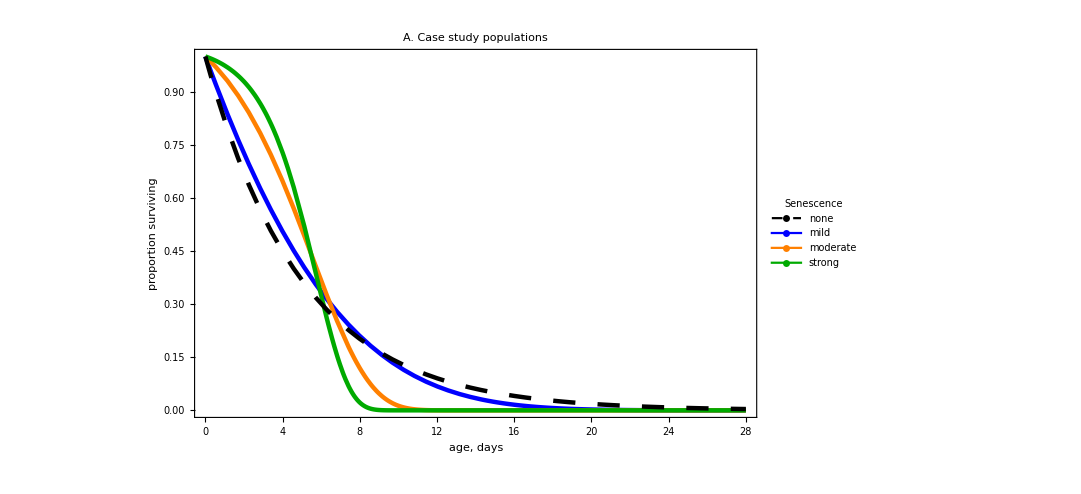

```mathematica
g3=Legended[Plot[{fGompertzSurvival[t,lAlpha[[1]],lBeta[[1]]],fGompertzSurvival[t,lAlpha[[2]],lBeta[[2]]],fGompertzSurvival[t,lAlpha[[3]],lBeta[[3]]],Exp[-(1/5)t]},{t,0,28},PlotRange->{Full,{0,1}},PlotStyle->{{Blue,Thickness[0.004]},{Orange,Thickness[0.004]},{Darker[Green],Thickness[0.004]},{Dashing[0.02],Black,Thickness[0.004]}},Frame->{True,True,False,False},FrameLabel->{"age, days","proportion surviving"},FrameStyle->Black,LabelStyle->{Black,FontSize->18},ImageSize->800,PlotLabel->"A. Case study populations"],Placed[LineLegend[{Directive[Black,Dashing[0.02]],Blue,Orange,Darker[Green]},{"none","mild","moderate","strong"},LegendMarkerSize->30,LegendMarkers->Graphics[{Thickness[0.05],Line[{{-10,0},{10,0}}]}],LabelStyle->{FontSize->18},LegendLabel->"Senescence"],{0.75,0.5}]]
```

```mathematica
lLenStudy=Table[3+i,{i,0,25,3}];
```

```mathematica
lLikelihoodStudyLengthCombined=Table[Table[ParallelTable[Quiet[fLikelihoodRatio[fGenerateSeriesGompertz[1000,Range@len,lAlpha[[i]],lBeta[[i]],0.03,3.18],Range@len,1000]],{k,1,500}],{i,1,3,1}],{len,lLenStudy}];
```

```mathematica
lLikelihoodStudyLengthCombined=lLikelihoodStudyLength3;
```

```mathematica
lPower=Table[fCalculatePowerCorrect[#,0.05]&/@lLikelihoodStudyLengthCombined[[All,i,All]],{i,1,3,1}];
lPower1=Thread[{lLenStudy,#}]&/@lPower;
```

```mathematica
lLikelihoodStudyLengthPartitioned =Table[Table[ fCalculatePowerCorrect[#,0.05]&/@Partition[lLikelihoodStudyLengthCombined[[All,i,All]][[j]],40],{j,1,Length@lLenStudy,1}],{i,1,3,1}];
```

```mathematica
lMedian=Table[Median/@lLikelihoodStudyLengthPartitioned[[i,All]],{i,1,3,1}];
lPower1=Thread[{lLenStudy,#}]&/@lMedian;
lError = Table[ErrorBar/@StandardDeviation/@lLikelihoodStudyLengthPartitioned[[i,All]],{i,1,3,1}];
```

StandardDeviation::shlen: The argument {} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

```mathematica
Needs["ErrorBarPlots`"]
```

ErrorBar::shdw: Symbol ErrorBar appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

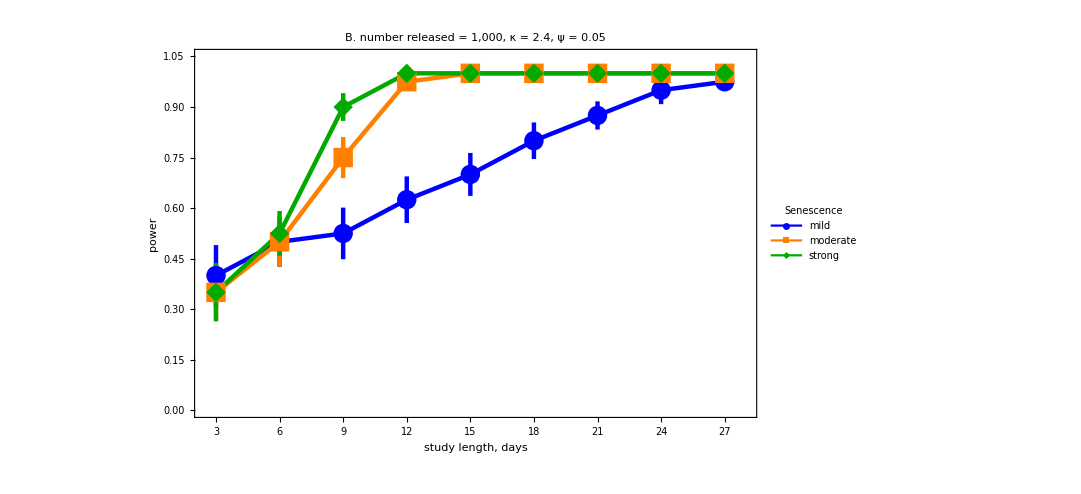

```mathematica
g1=Legended[Show[ErrorListPlot[Table[Thread[{lPower1[[i]],lError[[i]]}],{i,1,3,1}],Joined->True,PlotRange->{{2.5,28},{0,1.05}},Frame->{True,True,False,False},FrameLabel->{"study length, days","power"},FrameStyle->Black,LabelStyle->{Black,FontSize->18},PlotStyle->{{Blue,Thickness[0.004]},{Orange,Thickness[0.004]},{Darker[Green],Thickness[0.004]}},PlotLabel->"B. number released = 1,000, κ = 2.4, ψ = 0.05"],ListPlot[lPower1,PlotMarkers->{Automatic,20},PlotStyle->{Blue,Orange,Darker[Green]}],ImageSize->800],Placed[LineLegend[{Blue,Orange,Darker[Green]},{"mild","moderate","strong"},LegendMarkerSize->30,LegendLabel->"Senescence",LegendMarkers->{Automatic,30},LabelStyle->{FontSize->18}],{0.75,0.3}]]
```

```mathematica
lLikelihoodNumReleasedEqualCombined=Table[Table[ParallelTable[Quiet[fLikelihoodRatio[fGenerateSeriesGompertz[num,Range@9,lAlpha[[i]],lBeta[[i]],0.03,3.18],Range@9,num]],{k,1,500}],{i,1,3,1}],{num,lNumReleased1}];
```

```mathematica
lLikelihoodNumReleasedPartitioned =Table[Table[ fCalculatePowerCorrect[#,0.05]&/@Partition[lLikelihoodNumReleasedEqualCombined[[All,i,All]][[j]],40],{j,1,7,1}],{i,1,3,1}];
```

```mathematica
lMedianNumReleased=Table[Median/@lLikelihoodNumReleasedPartitioned[[i,All]],{i,1,3,1}];
lPowerNumReleased=Thread[{lNumReleased1,#}]&/@lMedianNumReleased;
lErrorNumReleased = Table[ErrorBar/@StandardDeviation/@lLikelihoodNumReleasedPartitioned[[i,All]],{i,1,3,1}];
```

```mathematica
Needs["ErrorBarLogPlots`"]
```

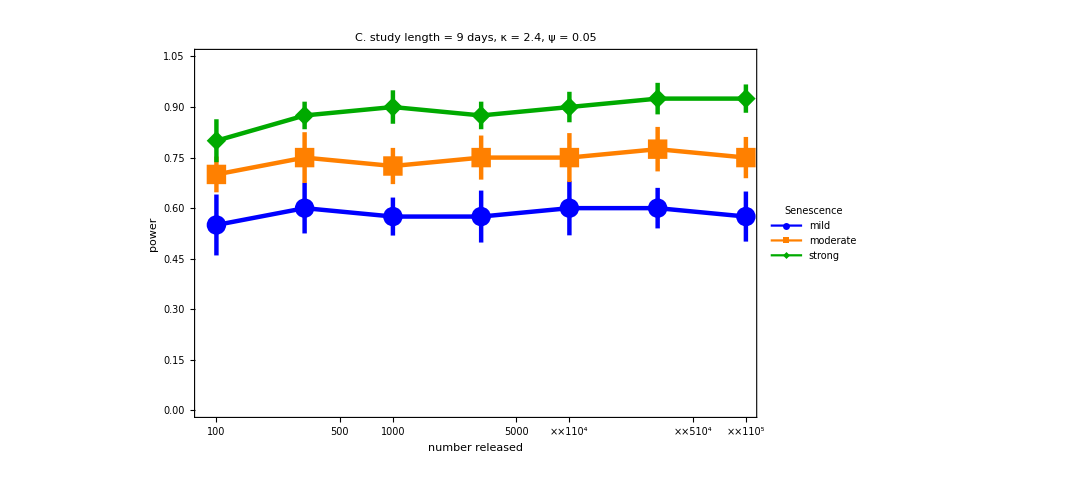

```mathematica
g2=Legended[Show[ErrorListLogLinearPlot[Table[Thread[{lPowerNumReleased[[i]],lErrorNumReleased[[i]]}],{i,1,3,1}],Joined->True,PlotRange->{Automatic,{0,1.05}},Frame->{True,True,False,False},FrameLabel->{"number released","power"},FrameStyle->Black,LabelStyle->{Black,FontSize->18},PlotStyle->{{Blue,Thickness[0.004]},{Orange,Thickness[0.004]},{Darker[Green],Thickness[0.004]}},PlotLabel->"C. study length = 9 days, κ = 2.4, ψ = 0.05"],ListLogLinearPlot[lPowerNumReleased,PlotMarkers->{Automatic,20},PlotStyle->{Blue,Orange,Darker[Green]}],ImageSize->800],Placed[LineLegend[{Blue,Orange,Darker[Green]},{"mild","moderate","strong"},LegendMarkerSize->30,LegendLabel->"Senescence",LegendMarkers->{Automatic,30},LabelStyle->{FontSize->18}],{0.75,0.25}]]
```

### Show exponential line as well

```mathematica
gFinal=Show[GraphicsRow[{g3,g1,g2}],ImageSize->2000]
```

```mathematica
Export["power-analysis-senescence.pdf",gFinal]
```

power-analysis-senescence.pdf

## For 15 days

```mathematica
lNumReleased1=Round[Table[(10^(2+0.5i)),{i,0,6}]]
```

{100,316,1000,3162,10000,31623,100000}

```mathematica
lLikelihoodNumReleasedEqual2=Table[Table[ParallelTable[Quiet[fLikelihoodRatio[fGenerateSeriesGompertz[num,Range@15,lAlpha[[i]],lBeta[[i]],0.03,3.18],Range@15,num]],{k,1,500}],{i,1,3,1}],{num,lNumReleased1}];
```

```mathematica
lLikelihoodNumReleasedEqual2>>lLikelihoodNumReleasedEqual2
```

```mathematica
lLikelihoodNumReleasedPartitioned =Table[Table[ fCalculatePowerCorrect[#,0.05]&/@Partition[lLikelihoodNumReleasedEqual2[[All,i,All]][[j]],40],{j,1,7,1}],{i,1,3,1}];
```

```mathematica
lMedianNumReleased=Table[Median/@lLikelihoodNumReleasedPartitioned[[i,All]],{i,1,3,1}];
lPowerNumReleased=Thread[{lNumReleased1,#}]&/@lMedianNumReleased;
lErrorNumReleased = Table[ErrorBar/@StandardDeviation/@lLikelihoodNumReleasedPartitioned[[i,All]],{i,1,3,1}];
```

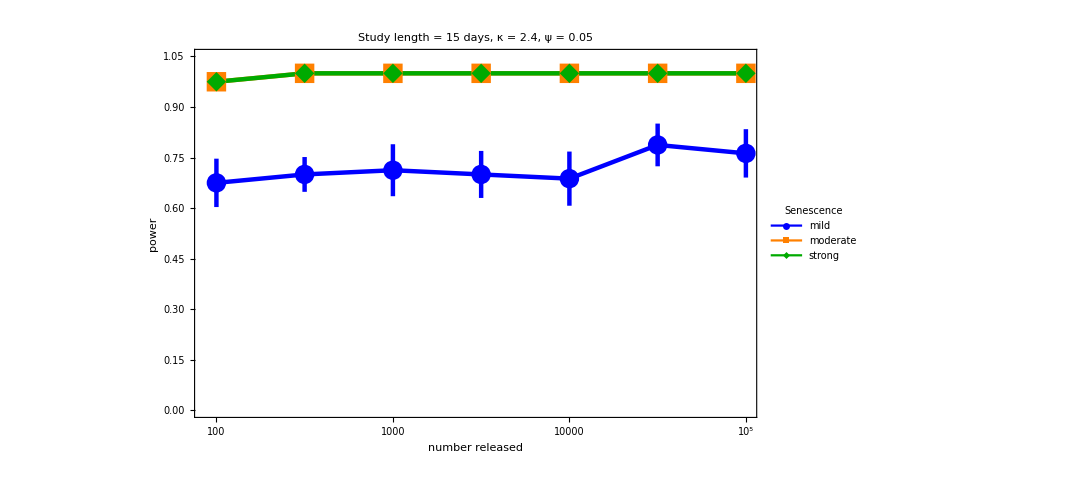

```mathematica
g2=Legended[Show[ErrorListLogLinearPlot[Table[Thread[{lPowerNumReleased[[i]],lErrorNumReleased[[i]]}],{i,1,3,1}],Joined->True,PlotRange->{Automatic,{0,1.05}},Frame->{True,True,False,False},FrameLabel->{"number released","power"},FrameStyle->Black,LabelStyle->{Black,FontSize->18},PlotStyle->{{Blue,Thickness[0.004]},{Orange,Thickness[0.004]},{Darker[Green],Thickness[0.004]}},PlotLabel->"Study length = 15 days, κ = 2.4, ψ = 0.05"],ListLogLinearPlot[lPowerNumReleased,PlotMarkers->{Automatic,20},PlotStyle->{Blue,Orange,Darker[Green]}],ImageSize->800],Placed[LineLegend[{Blue,Orange,Darker[Green]},{"mild","moderate","strong"},LegendMarkerSize->30,LegendLabel->"Senescence",LegendMarkers->{Automatic,30},LabelStyle->{FontSize->18}],{0.75,0.25}]]
```

```mathematica
Export["studyLength15Days.pdf",g2]
```

studyLength15Days.pdf